# Decaimiento del Higgs a dos fotones en VHDMM

```mathematica
Tabla=Import["/home/bastilo/Dropbox/ProyectoVectorDM/H->AA/BDCalchep/numerical.txt","numerical"];
```

Import::noelem: The Import element "numerical" is not present when importing as Text.

```mathematica
Tabla=Import["/home/bastilo/Dropbox/ProyectoVectorDM/H->AA/BDCalchep/numerical.txt"];
```

```mathematica
Tabla(*en fb*)
```

Mvp100              1.9490e+03      
Mvp200              7.2190e+00      
Mvp300              1.1760e+02       
Mvp400              1.8600e+02      
Mvp500              2.2260e+02       
Mvp600              2.4380e+02      
Mvp700              2.5700e+02       
Mvp800              2.6580e+02       
Mvp900              2.7190e+02       
Mvp1000             2.7630e+02

```mathematica
Tabla=Import["numerical.txt"];
```

Import::nffil: File not found during Import.

```mathematica
CppH=57.1; (*pb*)(*Total cross section pp->H*)
ΓHF1=1.7; (*GeV*)(*Full decay width Higgs*) (*PDG*)
ΓHF2=6.1; (*MeV*)(*Full decay width Higgs*)
      
BrHAA=2.27*10^-3;(*Branching fraction H->AA*)
```

```mathematica
ΓHAA=ΓHF2*10^-3*BrHAA;(*GeV*)
```

```mathematica
CppHAA=CppH*BrHAA(*GeV*)
```

0.129617

```mathematica
CppHAA
```

0.000790664

```mathematica
N[(1.9490e+03)/CppHAA]
```

4.53826 (1.949 e+3.)

```mathematica
N[0.117/CppHAA]
```

0.902659

```mathematica
Table1={{100,N[1.949/CppHAA]},{200,N[7.219/CppHAA]},{300,N[0.117/CppHAA]},{400,N[0.186/CppHAA]},{500,N[0.222/CppHAA]}};
Table2={{300,N[0.117/CppHAA]},{400,N[0.186/CppHAA]},{500,N[0.222/CppHAA]},{600,N[0.24380/CppHAA]},{700,N[0.25/CppHAA]},{800,N[0.26/CppHAA]}};
```

ListPlot::lpn: Tabladijetp is not a list of numbers or pairs of numbers.

ListPlot[Tabladijetp]

InterpolatingFunction[{{300., 800.}}, <>]

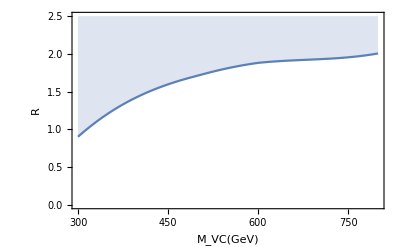

```mathematica
Gp=ListPlot[Tabladijetp]
Interp=Interpolation[Table2]
Dijet=Plot[Interp[x],{x,300,800},PlotRange->{{300,800},{0,2.5}},Frame->True,FrameLabel->{Subscript[M, VC][GeV],R},LabelStyle->Directive[Black,Bold,10],Filling->Top]
```

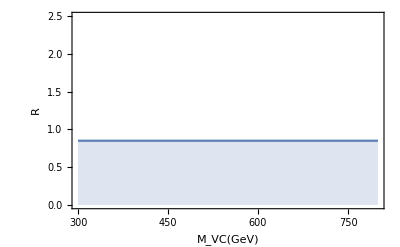

```mathematica
Diphotd=Plot[{0.85},{x,300,800},PlotRange->{{300,800},{0,2.5}},Filling->Bottom,Frame->True, FrameLabel->{Subscript[M, VC][GeV],R},LabelStyle->Directive[Black,Bold,10]]
```

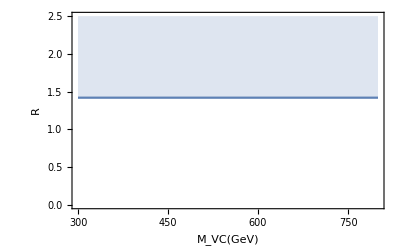

```mathematica
Diphotu=Plot[{1.42},{x,300,800},PlotRange->{{300,800},{0,2.5}},Filling->Top,Frame->True, FrameLabel->{Subscript[M, VC][GeV],R},LabelStyle->Directive[Black,Bold,10]]
```

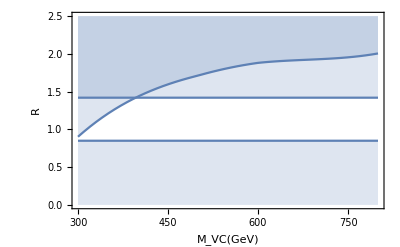

```mathematica
Show[Dijet,Diphotd,Diphotu]
```

```mathematica
0.18/(57*2.276*10^-3)
```

1.38748